# ADD L_* vs R_C

### Vorbereitungen

```mathematica
(* Prepare Export and metric units *)
SetDirectory[NotebookDirectory[]];
cm=72/2.54;
(* Epilabels von h-profiles.nb *)
(* Epic Epilog-Labels coming here, modified for the current problem:
   Featuring scaling and correct Inset (no rectangle nonrotated box).
 ASSUMING data be a list of X as variable, ideal for g00s. *)
ClearAll[EpiLabels]
EpiLabels[xpoint_, data_, labels_,axisratio_:1]:= 
With[{xpoints=If[Head@xpoint===List, xpoint, xpoint&/@ labels]}, (* erlaube Liste von xpoints *)
Inset[Rotate[Text[labels[[#]],Background -> White],
ArcTan@Re@N[(D[data⟦#⟧,X]/.{X-> xpoints⟦#⟧}) ] / axisratio] ,
{xpoints⟦#⟧, 0 +( data/.X-> xpoints⟦#⟧)⟦#⟧}
]& /@ Range@Length@data] (* 1: any value to introspect list*)
```

### Rechnung

```mathematica
Mpl=10^19; (*4d planck mass, Unit: GeV*)
```

```mathematica
Ω[d_] :=  (2 Pi^((d+1)/2))/Gamma[(d+1)/2]
Cn[n_] := (Ω[n+2]/Ω[2])^(1/(n+2))
Mstar[Rc_,n_]:=(Mpl^2/(Cn[n] (2π Rc)^n))^(1/(n+2))
```

```mathematica
auto = Automatic; hidden = Directive[FontOpacity->0,FontSize->0];
```

```mathematica
Table[Cn[n],{n,0,10}]//N
```

{1.,1.16245,1.203,1.19798,1.17502,1.14524,1.11345,1.08181,1.05131,1.02234,0.995038}

```mathematica
Table[CnEotWash[n],{n,0,10}]//N
```

{1.,1.84527,2.50663,3.01237,3.40502,3.71645,3.96858,4.17644,4.35055,4.49838,4.62541}

### Plot

```mathematica
funks[r_] = Table[Mstar[r,n],{n,0,5}]~Join~{10^4};
labels=Join[
{"No LXDs"},
Table["n="<>ToString@n,{n,1,3}],
{"...",""},
{"10 TeV (LHC)"}
]
```

{No LXDs,n=1,n=2,n=3,...,,10 TeV (LHC)}

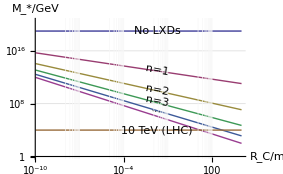

```mathematica
{rmin,rmax,Mmin,Mmax} = {10^(-10),10^4,1,10^20.5};
vline[xpos_] := Line@{{Log@xpos,Log@Mmin},{Log@xpos,Log@Mmax}}
figure=LogLogPlot[
Evaluate@funks@r,
{r,rmin,rmax},
PlotRange-> {Mmin,Mmax},
PlotRangeClipping->True,
AxesLabel-> {"R_C/m","M_*/GeV"},
Epilog-> {
EpiLabels[10^(-2), Log[funks[X]], labels,8]
    /. { Inset[t_, {x_,y_}] -> Inset[t,{-4,y}]},
(*Red,Thick,
vline[44 10^-6],
Text["44µm",Log@{0.5 10^-3,10^2}]
*)
},
GridLines->Automatic,
GridLinesStyle-> GrayLevel[0.97],
ImageSize-> 10cm
]
```

```mathematica
Export["../figures/ADD-fundamental-mass.pdf",figure]
```

../figures/ADD-fundamental-mass.pdf